Note: To run this file, first run /QTM/Hexagonal_Decomp, as it defines the real space displacement set, as well as computed the C6v eigenvectors used to decompose the measurement

### Hexagonal Grid

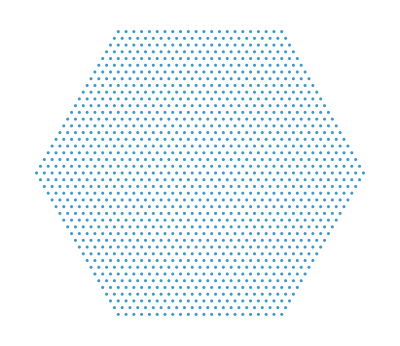

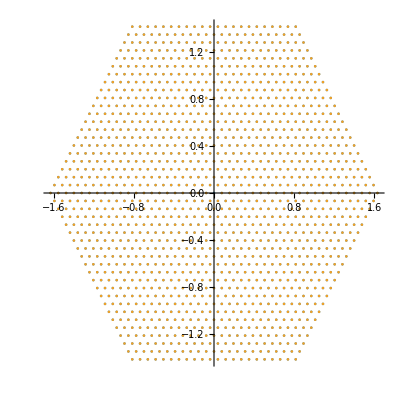

```mathematica
ℛUC=Polygon[1/(√3)Table[({Cos[2 Pi k/6+0π/2],Sin[2 Pi k/6+0π/2]}),{k,6}]];

h[x_,y_,0]:=Prepend[Table[{Cos[2 Pi k/6+0π/2]+x,Sin[2 Pi k/6+0π/2]+y},{k,6}],{0,0}]

h[x_,y_,n_]:=DeleteDuplicates[Flatten[Table[{Cos[2 Pi k/6+0π/2]+#1,Sin[2 Pi k/6+0π/2]+#2},{k,6}]&@@@h[x,y,n-1],1]]


ΛN=20;
UCmesh=2 √2 1/(√3)h[0,0,ΛN]/(ΛN+1);
kList=DeleteCases[UCmesh,{0,0}];
Show[Graphics[{EdgeForm[Thick],Transparent,ℛUC}],ListPlot[UCmesh,AspectRatio->1]]
ListPlot[{UCmesh,kList},AspectRatio->1]
```

### Parameters

```mathematica
w1=1;
w0=0.75w1;
μ=0.5;
mv=-0.5;
epsx=0.5;
epsy=-0.5;
a=1.42Sqrt[3];
gammaT=0.02 w1;
gammaS=0.02 w1;
biasEnergy=1 w1;  
dBias=0.001 w1;
thetaTwist=1.05Degree;
Ktheta=(4 Pi/(3 a)) 2 Sin[thetaTwist/2];
q0=Ktheta {0.3,0.4}√2;
qList=Table[RotationMatrix[2 Pi n/3].q0,{n,0,2}];

G[1]={0,0};

G[2]=(4 Pi/(3 a)) {-3/2,Sqrt[3]/2};

G[3]=(4 Pi/(3 a)) {-3/2,-Sqrt[3]/2};
```

### Order Parameters

```mathematica
DeltaT[k_]:=1.w1;
DeltaS[k_,λ_]:=1.w1*λ(k[[1]]);

(*DeltaS[k_,λ_]:=1. w1 *λ*k[[1]](k[[1]]^2-3k[[2]]^2)k[[2]](3k[[1]]^2-k[[2]]^2); (*A2*)*)
(*DeltaS[k_,λ_]:=1. w1 *λ*k[[1]](k[[1]]^2-3k[[2]]^2); (*B1*)
DeltaS[k_,λ_]:=1. w1 *λ*k[[2]](3k[[1]]^2-k[[2]]^2);(*B2*)*)
```

### Functions

```mathematica
ξT[k_,τ_]:=-μ+Norm[k];
ξS[k_,τ_]:=-μ+Norm[k];

DispersionS[k_,Δ_,τ_]:=Sqrt[ξS[k,τ]^2+Abs[Δ]^2];
DispersionT[k_,Δ_,τ_]:=Sqrt[ξT[k,τ]^2+Abs[Δ]^2];

uT[k_, Δ_, τ_]:=Sqrt[1/2(1+ξT[k,τ]/DispersionT[k,Δ,τ])];
uS[k_,Δ_,τ_]:=Sqrt[1/2(1+ξS[k,τ]/DispersionS[k,Δ,τ])];
vT[k_,Δ_,τ_]:=If[Δ==0,Sqrt[1/2 (1-ξT[k,τ]/DispersionT[k,Δ,τ])],Conjugate[Δ]/Abs[Δ]*Sqrt[1/2 (1-ξT[k,τ]/DispersionT[k,Δ,τ])]];

vS[k_,Δ_,τ_]:=If[Δ==0,Sqrt[1/2 (1-ξS[k,τ]/DispersionS[k,Δ,τ])],Conjugate[Δ]/Abs[Δ]*Sqrt[1/2 (1-ξS[k,τ]/DispersionS[k,Δ,τ])]];
th[k_]:=ArcTan[k[[1]],k[[2]]];

phi[j_]:=2Pi(j-1)/3;

M[k_,q_,r_,τ_,lambda_]:=Module[{kp,thetaK,thetaKp,thetaDelta,thetaSigma},(*Define the tip momentum and the respective angles*)kp=k+q;
thetaK=th[k];
thetaKp=th[kp];
thetaDelta=(thetaK-thetaKp)/2;
thetaSigma=(thetaK+thetaKp)/2;
Sum[(*First Term:uT uses tip momentum (kp),uS uses sample momentum (k)*)uT[kp,DeltaT[kp],τ]*uS[k,DeltaS[k,lambda],τ]*(w0*Cos[thetaDelta]+w1*τ*Cos[τ*phi[j]+thetaSigma])*Exp[I*τ*G[j].r]-(*Second Term:vT uses tip momentum (kp),vS uses sample momentum (k)*)Conjugate[vT[kp,DeltaT[kp],τ]]*vS[k,DeltaS[k,lambda],τ]*(w0*Cos[thetaDelta]+w1*τ*Cos[τ*phi[j]+thetaSigma])*Exp[I*τ*G[j].r],{j,1,3}]]
M[k_,{},r_,τ_,lambda_]:=0;
```

### Spectral functions

```mathematica
ElectronSpectral[xi_,delta_,omega_,gamma_]:=Module[{energy,u2,v2},energy=Sqrt[xi^2+Abs[delta]^2];
If[TrueQ[energy==0],Return[gamma/(Pi (omega^2+gamma^2))]];
u2=(1+xi/energy)/2;
v2=(1-xi/energy)/2;
(gamma/Pi)*(u2/((omega-energy)^2+gamma^2)+v2/((omega+energy)^2+gamma^2))];


AT[k_,omega_,tau_]:=ElectronSpectral[ξT[k,tau],DeltaT[k],omega,gammaT];

AS[k_,omega_,tau_,lambda_]:=ElectronSpectral[ξS[k,tau],DeltaS[k,lambda],omega,gammaS];


SpectralOverlap[k_,q_,tau_,lambda_?NumericQ,b_?NumericQ]:=Module[{kp,enT,enS,lo,hi,cuts,integrand,omega},If[TrueQ[b==0],Return[0.]];
kp=k+q;
enT=N[DispersionT[kp,DeltaT[kp],tau]];
enS=N[DispersionS[k,DeltaS[k,lambda],tau]];
lo=N[Min[-b,0.]];
hi=N[Max[-b,0.]];
cuts=Sort[DeleteDuplicates[Join[{lo,hi},Select[N[{-enS,enS,-b-enT,-b+enT}],lo<#<hi&]]]];
integrand[omega_?NumericQ]:=AT[kp,omega+b,tau]*AS[k,omega,tau,lambda];
Sign[b]*NIntegrate[integrand[omega],Evaluate[Prepend[cuts,omega]],Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->8,PrecisionGoal->6,MaxRecursion->20]];


SpectralDerivative[k_,q_,tau_,lambda_?NumericQ]:=(SpectralOverlap[k,q,tau,lambda,biasEnergy+dBias]-SpectralOverlap[k,q,tau,lambda,biasEnergy-dBias])/(2 dBias);


IntegrandPLUS[k_,q_,r_,lambda_?NumericQ]:=Abs[M[k,q,r,1,lambda]]^2*SpectralDerivative[k,q,1,lambda];

IntegrandMINUS[k_,q_,r_,lambda_?NumericQ]:=Abs[M[k,-q,r,-1,lambda]]^2*SpectralDerivative[k,-q,-1,lambda];


Signal[r_,lambda_?NumericQ]:=Sum[IntegrandPLUS[k,q,r,lambda]+IntegrandMINUS[k,q,r,lambda],{k,kList},{q,qList}];
```

### Data

```mathematica
kList=N[kList];
qList=N[qList];

If[$KernelCount==0,LaunchKernels[]];

DistributeDefinitions[Signal,IntegrandPLUS,IntegrandMINUS,SpectralDerivative,SpectralOverlap,AT,AS,ElectronSpectral,M,uT,uS,vT,vS,DispersionT,DispersionS,ξT,ξS,DeltaT,DeltaS,th,phi,G,kList,qList,gammaT,gammaS,biasEnergy,dBias,w0,w1,μ];

evA1=Eigenvectors[Subscript[P,A1]][[1]];
evA2=Eigenvectors[Subscript[P,A2]][[1]];
evB1=Eigenvectors[Subscript[P,B1]][[1]];
evB2=Eigenvectors[Subscript[P,B2]][[1]];

evE1=Take[Eigenvectors[Subscript[P,E1]],4];
evE2=Take[Eigenvectors[Subscript[P,E2]],4];

LaunchKernels[];
DistributeDefinitions[Signal,IntegrandPLUS,AT,AS,ElectronSpectral,M,uT,uS,vT,vS,DispersionT,DispersionS,ξT,ξS,DeltaT,DeltaS,th,phi,G,kList,qList,gammaT,gammaS,biasEnergy,w0,w1,μ,mv,epsx,epsy];

ConductanceVec[lambda_]:=ConductanceVec[lambda]=ParallelTable[Signal[r,lambda],{r,points}];

(*Reference strength to plot wrt*)
a10 = evA1.ConductanceVec[0];

SymmetryDecomp[lambda_]:=Module[{vec,a1,a2,b1,b2,e1,e2},vec=ConductanceVec[lambda];
a1=(evA1.vec)/a10;
a2=Chop[(evA2.vec)/a10,10^-6];
b1=Chop[(evB1.vec)/a10,10^-6];
b2=Chop[(evB2.vec)/a10,10^-6];
e1=Chop[((#.vec)/a10&)/@evE1,10^-6];
e2=Chop[-((#.vec)/a10&)/@evE2,10^-6];
{a1,a2,b1,b2,e1,e2}]

lambdaList=Range[0,0.240,0.02];

results=Monitor[Table[SymmetryDecomp[lambdaList[[i]]],{i,Length[lambdaList]}],Row[{"Lambda: ",Dynamic[i]," / ",Length[lambdaList],"   ",ProgressIndicator[Dynamic[i],{0,Length[lambdaList]}]}]];
A1vals=Abs[results[[All,1]]];
A2vals=Abs[results[[All,2]]];
B1vals=Abs[results[[All,3]]];
B2vals=Abs[results[[All,4]]];

E1vals=Norm/@Abs[results[[All,5]]];
E2vals=Norm/@Abs[results[[All,6]]];
```

### Plotting

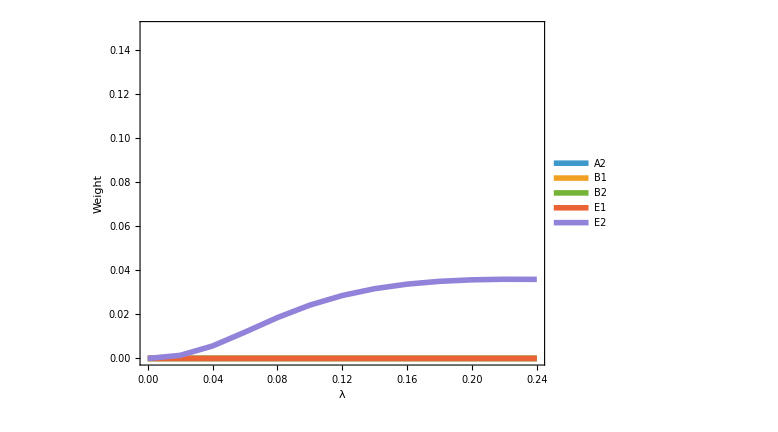

```mathematica
ListLinePlot[{Transpose[{lambdaList,A2vals}],Transpose[{lambdaList,B1vals}],Transpose[{lambdaList,B2vals}],Transpose[{lambdaList,E1vals}],Transpose[{lambdaList,E2vals}]},
PlotRange->{0,0.15},
PlotLegends->Placed[Style[#,20,FontFamily->"Times New Roman",Black]&/@{"A2","B1","B2","E1","E2"},{0.85,0.7}],
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thick],FrameLabel->{Style["λ",24,FontFamily->"Times New Roman",Black],Style["Weight",24,FontFamily->"Times New Roman",Black]},
LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],
PlotStyle->AbsoluteThickness[4],AspectRatio->0.75,ImageSize->Large]
```

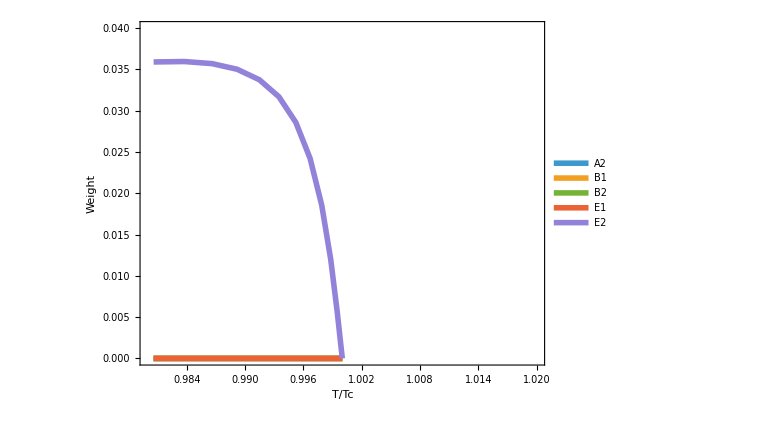

```mathematica
(*Converts plotting from order parameter strength to temperature*)
tList=1/(1+(ArcTanh[lambdaList]/1.74)^2);

tAbove=Subdivide[1.001,1.02,20];

normal=SymmetryWeights[ConductanceVector[1.1]];

normalVals={Abs[normal[[2]]],Abs[normal[[3]]],Abs[normal[[4]]],Norm[normal[[5]]],Norm[normal[[6]]]};

vals={A2vals,B1vals,B2vals,E1vals,E2vals};

idx=Select[Range[Length[tList]],0.98<=tList[[#]]<=1&];

plotData=Table[SortBy[Join[Transpose[{tList[[idx]],vals[[j,idx]]}],Table[{t,normalVals[[j]]},{t,tAbove}]],First],{j,5}];

ListLinePlot[plotData,PlotRange->{{0.98,1.02},{0,0.04}},PlotLegends->Placed[Style[#,20,FontFamily->"Times New Roman",Black]&/@{"A2","B1","B2","E1","E2"},{0.85,0.7}],
Frame->True,
Axes->False,
FrameStyle->Directive[Black,Thick],FrameLabel->{Style["T/Tc",24,FontFamily->"Times New Roman",Black],Style["Weight",24,FontFamily->"Times New Roman",Black]},
LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],
PlotStyle->AbsoluteThickness[4],AspectRatio->0.75,ImageSize->Large]
```